```mathematica
Lecture 15: Game Theory
```

Game Theory is the mathematical analysis of conflict and cooperation.

## Learning from experience

### Exercise Subsection

You and Colonel Blotto both have 100 soldiers which are to be distributed to 10 battleﬁelds. Secretly and independently, each commander divides the 100 forces into 10 parts and sends each part to a battleﬁeld. Ten ﬁghts take place, and the larger army wins at each battleﬁeld (neither army wins if the forces are the same size). The ultimate winner is the player who won the most battles. 

For example, if you use the strategy {10,10,10,10,10,10,10,10,10,10} and Colonel Blotto uses the strategy {2,11,11,11,11,11,11,11,11,10}, then Colonel Blotto wins because he won 8 battles to your 1.

a. Write a function named Blotto that inputs two lists of length 10 that sum to 100 (and has a check on the input pattern to make sure that the strategies have this property) and outputs 1 if the first strategy defeats the second, 0 if the strategies tie, and -1 otherwise.

b. The file at https://anthonymendes.github.io/Blotto.txt contains a list of 167 blotto strategies submitted by former game theory students.  Each strategy S1 in the list earns a total score by summing the value of Blotto when S1 competes against every other strategy in the list.  Sort the list from the best scoring to the worst scoring.

c. Find a strategy that would score higher than all other strategies if it were added to the list of 167 strategies and then the competition in part b was repeated.

```mathematica
Blotto[S1_List/;Length@S1==10&&Total@S1==100,S2_List/;Length@S2==10&&Total@S2==100]:=
Module[{wins=Count[S1-S2,_?Positive],loss=Count[S1-S2,_?Negative]},
Which[wins>loss,1,wins<loss,-1,True,0]]
```

```mathematica
Score[S1_]:=Total[Blotto[S1,#]&/@strategies]
{Score[#],#}&/@SortBy[strategies,Score]//Reverse
```

```mathematica
{Score[#],#}&/@SortBy[Join[strategies,{{7,7,18,8,20,2,8,19,5,6}}],Score]//Reverse
```

### Exercise Subsection

Each one of 100 people select a positive integer.  The winner (if there is one) is the person who selects the smallest number that is not selected by anyone else (see https://en.wikipedia.org/wiki/Unique_bid_auction ).  An optimal strategy is a probability vector {p_1,p_2,p_(3,)...,p_50} such that p_i is the to-be-determined probability that a player selects the integer i. 

Implement this idea to approximate the optimal strategy p:
1. Initialize p to be the vector of length 50 with each entry 1.  This will mean that every number 1 through 50 is equally likely to be selected.
2. Create a list L of 100 random integers between 1 and 50 with probability weighted using p (use RandomChoice[p->Range@n]).  This L models 100 people playing the game.
3. Select the smallest number in L that is not repeated, say it is m.
4. Update p by adding 1 position m in p.
5. Repeat steps 2 through 4 many times.  The approximate optimal strategy is the probability vector p/Total@p.

### Exercise Subsection

The integers in a random permutation of 1,2,...,100 are announced one at a time.  A player wins if they choose to “stop” after the integer 100 is announced.  However, the following strategy must be used:

1. An integer R is chosen before any numbers are announced. 
2. The first R integers announced are automatically rejected.
3. After that, “stop” is said if an integer is announced that is the largest integer announced so far.

The goal is to find the optimal value of R.  Approximate this value of R using the following steps:

1. Define a function GoodRValues[L_] that has input a permutation L of 1,...,100 and output the list integers R that will identify 100 using the above scheme.
2. Run GoodRValues many times on RandomSample@Range@100 to find the integer R that is most likely to identify 100.

```mathematica
GoodRValues[L_]:=Select[Range@100,Module[{p=First@FirstPosition[L,100]},#<p&&Max[L[[;;#]]]>Max[L[[#+1;;p-1]]]&]]
```

```mathematica
SortBy[Table[GoodRValues@RandomSample@Range@100,10000]//Flatten//Tally,Last]//Reverse
```

{{36,3758},{35,3758},{37,3753},{40,3746},{41,3743},{39,3738},{38,3729},{42,3724},{34,3723},{33,3707},{43,3699},{31,3693},{32,3691},{44,3687},{30,3686},{45,3669},{46,3641},{29,3638},{28,3632},{47,3627},{48,3616},{27,3616},{26,3589},{49,3573},{25,3566},{50,3550},{51,3509},{24,3505},{52,3479},{53,3474},{23,3451},{54,3437},{22,3397},{55,3396},{21,3343},{56,3335},{20,3291},{57,3270},{58,3230},{19,3196},{59,3157},{18,3134},{60,3100},{17,3070},{61,3049},{62,2991},{16,2963},{63,2910},{15,2884},{64,2834},{65,2803},{14,2795},{66,2762},{67,2701},{13,2700},{68,2662},{12,2604},{69,2597},{70,2526},{11,2502},{71,2456},{72,2385},{10,2379},{73,2323},{74,2257},{9,2229},{75,2151},{8,2094},{76,2090},{77,2043},{78,1963},{7,1934},{79,1886},{80,1817},{6,1738},{81,1734},{82,1654},{5,1563},{83,1548},{84,1466},{4,1382},{85,1368},{86,1287},{87,1185},{3,1148},{88,1099},{89,1006},{90,920},{2,839},{91,820},{92,737},{93,644},{94,566},{1,530},{95,483},{96,390},{97,306},{98,205},{99,90}}

## Matrix Games

### Exercise Subsection

A matrix game on a matrix A has two players: a row player and a column player.  The row player secretly selects a row r, the column player secretly selects a column c.  When choices are revealed, the row player earns A[[r,c]] from the column player.  Therefore the row player wants to maximize A[[r,c]] and the column player wants to minimize A[[r,c]].

For example, the matrix in the next cell models “rock, paper, scissors” with the winner earning $1 from the loser.

```mathematica
A={{0,-1,1},{1,0,-1},{-1,1,0}};
TableForm[A,TableHeadings->{{"Rock","Paper","Scissors"},{"Rock","Paper","Scissors"}}]
```

| Rock | Paper | Scissors
Rock | 0 | -1 | 1
Paper | 1 | 0 | -1
Scissors | -1 | 1 | 0

An optimal strategy for the row (or column) player is a probability vector that gives the probability that a rational and intelligent player should play each row.  Finding optimal row and column strategies can be found using the code in the next cell.

```mathematica
RowStrategy[P_]:=Module[{d=Dimensions@P,L},(L=LinearProgramming[Table[1,d[[1]]],Transpose@P+1-Min@P,Table[1,d[[2]]]])/Total@L]
ColStrategy[P_]:=RowStrategy@Transpose[-P]
```

For example, for the “rock, paper, scissors” matrix A defined above, the next cell gives the (somewhat obvious) optimal strategies for the row and column player:

```mathematica
RowStrategy@A
ColStrategy@A
```

{1/3,1/3,1/3}

{1/3,1/3,1/3}

### Exercise Subsection

There are occasionally penalty kicks in soccer. Each penalty kick involves only a kicker and a goalie.  1417 actual penalty kicks in professional soccer matches were analyzed to arrive at this matrix game, where the kicker is the row player, the goalie is the column player, and the entries give the probability of a goal.

```mathematica
soccer={{.58,.95},{.93,.7}};
TableForm[soccer,TableHeadings->{{"Kick right","Kick left"},{"Anticipate right","Anticipate left"}}]
```

| Anticipate right | Anticipate left
Kick right | 0.58 | 0.95
Kick left | 0.93 | 0.7

Give the optimal strategies for the kicker and the goalie.

### Exercise Subsection

Morra is a rock-paper-scissors like hand game played between two players (see https://en.wikipedia.org/wiki/Morra_(game) ).  Here is one variant: each player shows 0,1,2,3,4, or 5 fingers on a hand and simultaneously guesses the total number of fingers shown between both players (a number between 0 and 10).  If exactly one player correctly guesses the total number of fingers, that player earns 1 from the loser.  

Therefore the strategies for each player are pairs {f,g} where f is the number of fingers shown and g is the number of fingers guessed.  Do the following to solve the game:
1. Create a list named strategies containing all pairs {f,g} where f is any number 0,...,5 and g is any number 0,...,10.
2. Define a function Payoff with input strategies s1 and s2 in strategies and output 1 if s1 wins, -1 if s2 wins, and 0 otherwise.
3. Create a payoff matrix s1, s2 entry given by Payoff[s1,s2] where s1 and s2 range over all strategies.
4. Apply RowStrategy (as defined in Lecture15) to solve the matrix game.

```mathematica
strategies=Tuples[{Range[0,5],Range[0,10]}];
Payoff[s_,t_]:=Which[Last@t==Last@s,0,First@s+First@t==Last@s,1,First@s+First@t==Last@t,-1,True,0]
A=Table[Payoff[s,t],{s,strategies},{t,strategies}];
Cases[Transpose@{RowStrategy@A,strategies},{a_,b_}/;a!=0]
```

{{1/6,{0,0}},{1/6,{1,6}},{1/6,{2,6}},{1/6,{3,4}},{1/6,{4,7}},{1/6,{5,7}}}

### Exercise Subsection

Rose secretly writes down a number between 1 and n. Colin repeatedly guesses Rose's number until guessing correctly.  After an incorrect guess of k, Rose tells Colin if his guess is higher or lower than k . At the end of the game, Colin pays Rose the number of guesses it took to ﬁnd Rose's secret number.

The strategies for Rose are the numbers 1 through n.  The strategies for Colin are the permutations of 1,...,n where the permutation gives the sequence of guesses (with guesses that are known to be wrong skipped). 

Find the optimal row (Rose) and column (Colin) strategies in the case n = 6 by doing the following:
1. Define a function Payoff[r_,col_] with input an integer r between 1 and 6 and a permutation col of 1,...,6 and output the number of guesses taken to find r using the strategy col.  I was able to do this efficiently by recursively defining Payoff.
2. Create the matrix with entries Payoff[r_,col_] where r, col range over all possible strategies.
3. Apply RowStrategy and ColStrategy (as defined in Lecture15) to solve the matrix game.

It is an open problem to find an optimal column strategy for this game for large n.

```mathematica
Payoff[k_,col_]:=1+Module[{g=col[[1]]},Which[g==k,0,g<k,Payoff[k,Cases[col,a_/;a>g]],g>k,Payoff[k,Cases[col,a_/;a<g]]]]
A=Table[Payoff[k, col], {k, Range@6}, {col, Permutations@Range@6}] ;
A//GameSolution
```

### Exercise Subsection

A two player game can be played on a graph G in this way:  Both players select vertices in G.  If the vertices are connected, then the first player earns 1 from the second player, otherwise the payoff is 0.  This is a matrix game with payoff matrix equal to AdjacencyMatrix@G.  Find optimal strategies for the row and column players when playing this game on each of the graphs in the list below:

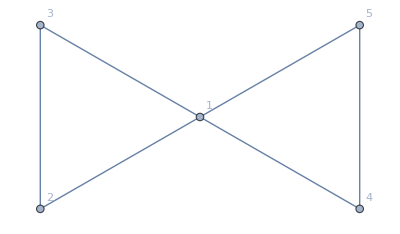
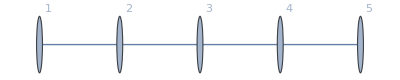
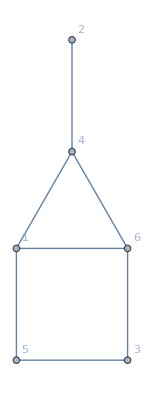
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

### Exercise Subsection

A random integer r between 1 and 100 is selected.  Two players both try to guess r, and the player that is closest without going over is the winner (like the Price is Right game show). 

a. Write a function named Payoff[i_,j_,r_] that has input the guess i for the first player, the guess j for the second player, the integer r between 1 and 100.  The output should be 1 if the first player wins, -1 if the second player wins, and 0 if there is a tie or neither player wins.

```mathematica
Payoff[i_,j_,r_]:=Which[i==j,0,r<Min[{i,j}],0,i<=r<j,1,i<j<=r,-1,j<=r<i,-1,j<i<=r,1]
```

b.  Once the function Payoff has been defined, then the expected payoff matrix A can be defined with the code in the next cell:

```mathematica
ExpectedPayoff[i_,j_]:=Sum[Payoff[i,j,r]/100,{r,100}]
A=Table[N@ExpectedPayoff[i,j],{i,100},{j,100}];
```

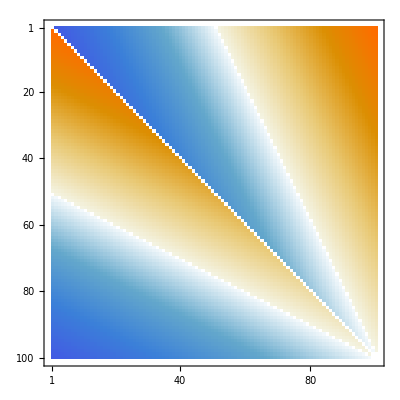

-1+10/(√(100-x))

```mathematica
A//MatrixPlot
F[x_]:=Which[x<=0,0,x>3/4,1,True,1/Sqrt[1-x]-1]
y[x]/.First@DSolve[{0==(2x−200)y'[x]+1+y[x],y[0]==0},y,x]//Simplify
```

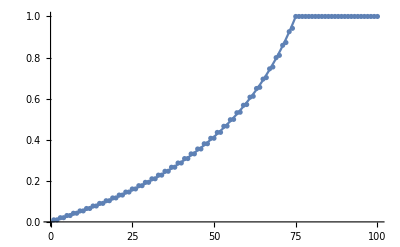

```mathematica
Show[ListPlot[Accumulate[First@GameSolution@N@A//Chop]],Plot[-1+10/(√(100-x)),{x,0,75}]]
```

### Exercise Subsection

fictitious play

## Nonzero sum games

### Exercise Subsection

The prisoner’s dilemma is a two player game where each player can cooperate for mutual benefit or betray their partner for individual reward.  The payoffs to each player are given in the table below, with the entries giving the payoff to the row and column player, respectively.

```mathematica
dilemma={{{1,1},{0,3}},{{3,0},{-1,-1}}};
TableForm[ToString/@#&/@dilemma,TableHeadings->{{"Cooperate","Betray"},{"Cooperate","Betray"}}]
```

| Cooperate | Betray
Cooperate | {1, 1} | {0, 3}
Betray | {3, 0} | {-1, -1}

```mathematica
PrisonerCompete[F_,G_,History_]:=
```

```mathematica
History={"C","D","C","C"}
```

{C,D,C,C}

### Exercise Subsection

Chicken is a two player game

## The Shapley value

### Exercise Subsection

Four shareholders in a company each have a certain number of votes:

```mathematica
Shareholders={{"Alice",1},{"Bob",2},{"Carl",3},{"Dana",4}};
```

To pass a measure, more than 5 shares are needed.  How much power does each member have? 

The Shapley value provides an answer:  Consider all Permutations of the shareholders.  For each permutation, read from left to right.  The first time that the accumulated vote total surpasses 5, the voter that changed the vote from losing to winning earns one point.  The average point total for each voter is the Shapley value.  

Understand how the code in the next cell finds this Shapley value:

```mathematica
WinningVoter[L_]:=L[[SelectFirst[Range@4,Total[L[[;;#,2]]]>5&],1]]
Table[{voter,N@Count[WinningVoter/@Permutations@Shareholders,voter]/4!},{voter,First/@Shareholders}]//TableForm
```

Alice | 0.0833333
Bob | 0.25
Carl | 0.25
Dana | 0.416667

### Exercise Subsection

The 1958 Treaty of Rome gave the original six countries in the European Union these votes:

```mathematica
EU={{"France", 4}, {"Germany",4},{"Italy", 4}, {"Belgium",2},{"Netherlands",2},{"Luxembourg",1}};
```

A coalition containing at least 4 members and at least 12 votes can pass a resolution.  What is the Shapley value for each country?

In other words, consider all permutations  of EU members.  For each permutation, read from left to right.  The first time that the accumulated coalition gains the power to pass a resolution, the country that changed the vote from losing to winning earns one point.  The average point total for each country is the Shapley value.

### Exercise Subsection

A family of 2 parents and 3 children make decisions on what to eat for dinner by voting.  Each parent gets 2 votes, each child 1 vote, and at least 4 votes are needed to win.  What is the Shapley value for each person?

### Exercise Subsection

Cities within Nassau county (in New York state) were given the number of votes in the next cell, with 16 votes needed to pass a measure.  What is the Shapley value for each city?

```mathematica
Nassau={{"Hempstead1",9},{"Hempstead2",9},{"North Hempstead",7},{"Oyster Bay",3},{"Glen Cove",1},{"Long Beach",1}};
```

### Exercise Subsection

The next cell lists all states (and the District of Columbia) together with their number of votes in the Electoral College.

```mathematica
College={{"Alabama",9} ,{"Alaska",3},{"Arizona",11},{"Arkansas",6},{"California",54},{"Colorado",10},{"Connecticut",7},{"Delaware",3},{"District of Columbia",3},{"Florida",30},{"Georgia",16},{"Hawaii",4},{"Idaho",4},{"Illinois",19},{"Indiana",11},{"Iowa",6},{"Kansas",6},{"Kentucky",8},{"Louisiana",8},{"Maine",4},{"Maryland",10},{"Massachusetts",11},{"Michigan",15},{"Minnesota",10},{"Mississippi",6},{"Missouri",10},{"Montana",4},{"Nebraska",5},{"Nevada",6},{"New Hampshire",4},{"New Jersey",14},{"New Mexico",5},{"New York",28},{"North Carolina",16},{"North Dakota",3},{"Ohio",17},{"Oklahoma",7},{"Oregon",8},{"Pennsylvania",19},{"Rhode Island",4},{"South Carolina",9},{"South Dakota",3},{"Tennessee",11},{"Texas",40},{"Utah",6},{"Vermont",3},{"Virginia",13},{"Washington",12},{"West Virginia",4},{"Wisconsin",10},{"Wyoming",3}};
```

To elect a president, more than 269 votes are needed.  Estimate the Shapley value for each state using the following idea:
1. Randomly permute College using RandomSample@College
2. Find the state that changes the accumulated vote total in the random permutation from less than or equal to 269 to greater than 269. 
3. Give that state one point. 
4. Repeat steps 1,2,3 many times over, and then find the average point total for each state.